Comparing behaviour of linear and non-linear differential equations describing pendulum movement

by Claudio Mora Díaz
Pontificia Universidad Católica de Chile
Escuela de Ingeniería

## Introduction

Differential equations are use to model a great variety of physical systems based on the analysis of how things change over time. Due to its nature, many differential equations are not easily solved by analytic methods, furthermore, in some cases such solution does not exist or can not be represented in terms of known mathematical expressions (such as polynomials, trigonometric functions, logarithmics, etc).

In this document, I will study the behaviour of a particular set of differential equations. The first one allows to be solved analytical, the second however, will need a numerical approach. These equations model the movement of a simple pendulum; a system consisting of a mass m swinging in a 2D space around a fixed vertical axis, attached to a massless rod (not flexible) of length L [1].

One of the simplest forms of the model considers no air resistance and no external forces being applied to the mass. It can be expressed as:

Where θ=θ(t) is the counterclockwise angle that the rod makes with the vertical at time t, and g is the acceleration given by gravity. Due to the fact that there is no air resistance, nor a force being applied, the system is independent of the mass.

Despite all the assumptions and simplifications, the equation in (1) can be hard to solve analytical. Hence, we transform the model to be linear:

This approximation of  comes from taking the first term in the Taylor series for  and it is usually made for small values of θ. We can, in fact, test if this is a valid approximation by plotting the percent error in a small interval:

```mathematica
(* Approximation error function *)
δ[θ_]:=Abs[(Sin[θ]-θ)/θ]*100 
(* Plotting the function *)
Plot[{δ[θ],θ,Sin[θ]},{θ,0,Pi/3},
(* Adding some aesthetic elements *)
PlotLabels->"Expressions",PlotLabel->Style["Percent error",14,FontFamily->"Times New Roman"]]
```

-Graphics-

From the graphic, it is visible that θ and sin(θ) are similar in this interval  with a small percentual error. Thus, it is expected that the behaviour of a “linear pendulum” is similar to that of a “sinusoidal pendulum”.

## Creating the linear pendulum

### Analytical solution

To create the pendulum, we first need to solve the differential equation to obtain the function modeling the angle between the rod and the vertical axis. 

We will obtain the solution for the linear equation by assigning specific values to different important parameters: first, we define g, which is easily recognized as the acceleration due to gravity, hence we say g=9.81 m/s^2 is a good approximation.

As for the rest of parameters, that is, the length of the rod, the starting angle, and the initial velocity, we will let them expressed by arbitrary names L,α,ω respectively.

```mathematica
linearsol=DSolveValue[{θ''[t]+9.81/L θ[t]==0,θ'[0]==ω,θ[0]==α},θ,t]
```

Function[{t},1. α Cos[(3.13209 t)/(√L)]+0.319275 √L ω Sin[(3.13209 t)/(√L)]]

We will now assume specific values for the parameters, let’s say L=6,α=π/6 and ω=0. With this, we can create the function for the angle given by time.

```mathematica
linearθ[t_]=linearsol[t]/.{L->6,α->Pi/6,ω->0}
```

0.+0.523599 Cos[1.27867 t]

Plotting this expression for the first 20 seconds:

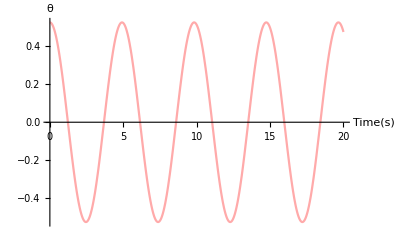

```mathematica
Plot[linearθ[t],{t,0,20},AxesLabel->{"Time(s)",θ},PlotStyle->Lighter[Pink]]
```

Notice that the maximum amplitude for the function does not change, this is expected as there are no external forces draining energy from the system.

### Graphics

We can now visualize all the elements from the system. I will start by creating the roof and the vertical axis from which the angle θ is measured.

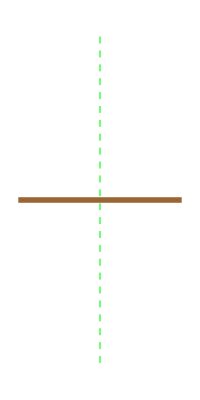

```mathematica
roof=Graphics[{Brown,Thickness[0.01],Line[{{-5,0},{5,0}}]}];
verticalaxis=Graphics[{Green,Dashed,Thickness[0.002],Line[{{0,10},{0,-10}}]}];
Show[roof,verticalaxis,PlotRange->{{-5,5},{0,-10}}]
```

To properly get the pendulum (rod and mass), we will need to know its coordinates. Assuming the origin (0,0) is at the intersection of the roof with the vertical axis, we notice (with a bit of trigonometry) that its coordinates are given by:

Where L is the length of the rod. With this, we can look at the position of the pendulum at t=0.

```mathematica
linearX[t_]:=6*Sin[linearθ[t]]
linearY[t_]:=-6*Cos[linearθ[t]]
Print["Position of the mass at t=0: ","{",linearX[0],",",linearY[0],"}"]
```

Position of the mass at t=0: {3.,-5.19615}

To visualize it, we just need to create the mass, which I will show as a circle, and the rod will be shown as a line connecting the origin and the center of the mass.

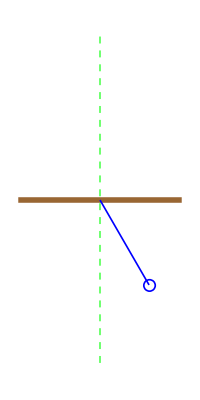

```mathematica
linearpendulum[t_]=Graphics[{Blue,Thickness[0.003],Circle[{linearX[t],linearY[t]},0.35],Line[{{0,0},{linearX[t],linearY[t]}}]}];
Show[roof,verticalaxis,linearpendulum[0],PlotRange->{{-5,5},{0,-10}}]
```

To see the full movement, we just need to animate this.

```mathematica
Animate[Show[roof,verticalaxis,linearpendulum[t],PlotRange->{{-5,5},{0,-10}}],{t,0,10},AnimationRate->2.5,SaveDefinitions->True]
```

## Creating the sinusoidal pendulum

### Numerical solution

It has been previously mentioned that the original equation at (1) is not easy to solve analiticaly, hence, we will take a numerical approach Mathematica offers a command that does all the needed math for us. Thus, we just need to repeat the process from the previous section. Assuming L=6, ω=0 and α=π/6.

```mathematica
sinsol=NDSolve[{θ''[t]+9.81/6*Sin[θ[t]]==0,θ'[0]==0,θ[0]==Pi/6},θ,{t,0,60}]
```

{{θ→InterpolatingFunction[…]}}

```mathematica
sinθ[t_]=First[θ[t]/.sinsol];
```

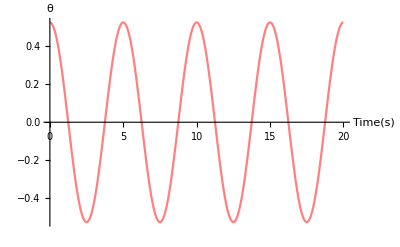

```mathematica
Plot[sinθ[t],{t,0,20},AxesLabel->{"Time(s)",θ},PlotStyle->Pink]
```

### Graphics

Both pendulums hang from the same roof and move around the same vertical axis. We just need to create the new pendulum and add it to the system.
As done before, we get the X and Y coordinates by the following equations:

Where L=6 is the length of the rod and θ(t) is now the angle obtained from solving the sinusoidal equation.

```mathematica
sinX[t_]:=6*Sin[sinθ[t]]
sinY[t_]:=-6*Cos[sinθ[t]]
Print["Position of the mass at t=0: ","{",sinX[0],",",sinY[0],"}"]
```

Position of the mass at t=0: {3.,-5.19615}

And we create the graphic object of the pendulum:

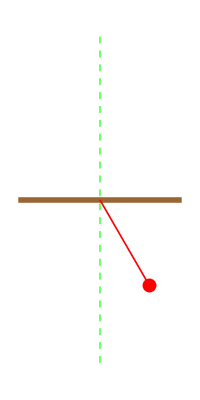

```mathematica
sinpendulum[t_]=Graphics[{Red,Thickness[0.003],PointSize->0.025,Point[{sinX[t],sinY[t]}],Line[{{0,0},{sinX[t],sinY[t]}}]}];
Show[roof,verticalaxis,sinpendulum[0],PlotRange->{{-5,5},{0,-10}}]
```

Animating this result

```mathematica
Animate[Show[roof,verticalaxis,sinpendulum[t],PlotRange->{{-5,5},{0,-10}}],{t,0,10},AnimationRate->2.5,SaveDefinitions->True]
```

## Comparison

### Original problem

Finally, with both solutions obtained, we can compare different things. I will start taking a look at the function obtained that models the angle θ. Plotting said function for both approaches at the same time:

```mathematica
Plot[{linearθ[t],sinθ[t]},{t,0,20},AxesLabel->{"Time(s)",θ},PlotLabels->{"Linear","Sinusoidal"},PlotStyle->{Lighter[Pink],Pink},ImageSize->500]
```

-Graphics-

As expected, the two solutions differ from each other. The linear approach seems to be having a slightly faster period which results in its plot being more horizontally compressed.

We can also animate both pendulums at the same time, making the difference more obvious to the eye:

```mathematica
Animate[Show[roof,verticalaxis,linearpendulum[t],sinpendulum[t],PlotRange->{{-5,5},{0,-10}},PlotLegends->Automatic],{t,0,30},AnimationRate->2.5,SaveDefinitions->True]
```

To see how much the result varies we can use the same technique of the percent error (assuming the numerical solution as the correct answer):

```mathematica
Δ[t_]:=Abs[(linearθ[t]-sinθ[t])/sinθ[t]]*100
LogPlot[{linearθ[t],sinθ[t],Δ[t]},{t,0,30},AxesLabel->{"Time(s)",θ},PlotLabels->"Expressions",ImageSize->600,PlotLabel->Style["Logarithmically scaled percent error",18,FontFamily->"Times New Roman"]]
```

-Graphics-

We see two important things: the first is that the maximum value of the error is increasing with each cycle of the pendulum, and that the range between the maximum and the minimum value is decreasing.

### Changing the starting angle

As we have established, the approximation of  is good for small values of θ. Now, we will see if not following this requisite affects the results in a significant way. For this, we will  remove the roof and give a starting angle α=4π/6.

First we get the solutions for the functions:

```mathematica
linear2[t_]=linearsol[t]/.{L->6,α->4Pi/6,ω->0};
sin2[t_]=First[θ[t]/.NDSolve[{θ''[t]+9.81/6*Sin[θ[t]]==0,θ'[0]==0,θ[0]==4Pi/6},θ,{t,0,60}]];
```

Getting the X and Y coordinates of each pendulum.

```mathematica
linearX2[t_]:=6*Sin[linear2[t]]
linearY2[t_]:=-6*Cos[linear2[t]]

sinX2[t_]:=6*Sin[sin2[t]]
sinY2[t_]:=-6*Cos[sin2[t]]
```

Pendulums as graphic objects

```mathematica
linearpendulum2[t_]=Graphics[{Blue,Thickness[0.003],Circle[{linearX2[t],linearY2[t]},0.35],Line[{{0,0},{linearX2[t],linearY2[t]}}]}];

sinpendulum2[t_]=Graphics[{Red,Thickness[0.003],PointSize->0.025,Point[{sinX2[t],sinY2[t]}],Line[{{0,0},{sinX2[t],sinY2[t]}}]}];
```

And finally animating both pendulums:

```mathematica
Animate[Show[verticalaxis,linearpendulum2[t],sinpendulum2[t],PlotRange->{{-7,7},{5,-10}},PlotLegends->Automatic],{t,0,30},AnimationRate->2.5,SaveDefinitions->True]
```

Acquiring the same plots from the previous version:

```mathematica
Plot[{linear2[t],sin2[t]},{t,0,20},AxesLabel->{"Time(s)",θ},PlotLabels->{"Linear","Sinusoidal"},PlotLabel->Style["Pure functions",18,FontFamily->"Times New Roman"],PlotStyle->{Lighter[Pink],Pink},ImageSize->500]
Δ2[t_]:=Abs[(linear2[t]-sin2[t])/sin2[t]]*100
LogPlot[{linear2[t],sin2[t],Δ2[t]},{t,0,30},AxesLabel->{"Time(s)",θ},PlotLabels->"Expressions",ImageSize->600,PlotLabel->Style["Logarithmically scaled percent error",18,FontFamily->"Times New Roman"]]
```

-Graphics-

-Graphics-

It is clear that the behaviour of the linear approximation is completely different from the sinusoidal function. This results in an error function with more chaotic spikes.

## References

Henry Edwards, Charles, E. Penney, David and Calvis, David. Differential Equations and Boundary Value Problems. 5th. s.l. : Pearson, 2019.